## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"];
SetDirectory@NotebookDirectory[];
```

```mathematica
RuleEigenApprox={λ->l (l+1)-s (s+1)};
RuleNearApprox={x^(n_.) (ω̄)^(m_.)->0,x^(n_.) (Ω̄)^(m_.)->0,x^(n_.) χ^(m_.)->0};
RuleFarApprox={n_. x+τ:>n x,n_. x+y_:>n x/;FreeQ[y,x]};
RuleAbsorbC={a_ C[i_]:>C[Unique[]]/;FreeQ[a,x]};
RuleFuncExpansion=
{LegendreP[ν_,μ_,z_]:>((z+1)/(z-1))^(μ/2) Hypergeometric2F1[-ν,ν+1,1-μ,(1-z)/2]};
```

```mathematica
RuleNegativeΓ={Gamma[l α_.+β_.]/Gamma[l γ_.+σ_.]:>(γ (-1)^(l γ+σ-l α-β) Gamma[-l γ-σ+1])/(α Gamma[-l α-β+1])/;Negative[α]&&Negative[γ]};
RuleExtraΓ={Gamma[2+l+x_]/Gamma[1-l+x_]:>((-1)^(l+1) (l+1) x (k^2-x^2)k1l)/l};
```

## Equations and definitions

```mathematica
Clear[Δ,Σ,ρ,𝒦,𝒬];
Δ[r_]=r^2-2 M r+a^2;
Σ[r_,θ_]=r^2+a^2 Cos[θ]^2;
ρ[r_,θ_]:=r+I a Cos[θ];
𝒦[r_]=(r^2+a^2) ω-a m;
𝒬[θ_]=a ω Sin[θ]-m Csc[θ];
```

```mathematica
𝒬'[θ]+𝒬[θ]Cot[θ]//Simplify
```

2 a ω Cos[θ]

```mathematica
Clear[EqTeukolskyRadial𝒦];
EqTeukolskyRadial𝒦=(x (x+τ))^-s D[((x (x+τ))^(s+1) ℛ'[x]), x]+((κ^2-ⅈ s (2 x+τ) κ)/(x (x+τ))-λ+4 ⅈ s ω̄ (1+x)) ℛ[x];
```

```mathematica
Clear[Rule𝒦Radial,EqTeukolsky];
Rule𝒦Radial={κ->Collect[Expand[𝒦[rp (1+x)]]/rp/.{c_ a^2+c_ rp^2->c 2 M rp}/.{a->2 M Ω̄,ω->(ω̄)/rp},M,Factor]/.{ω̄-m Ω̄->(χ rp)/(2 M)}};
EqTeukolsky=EqTeukolskyRadial𝒦/.Rule𝒦Radial;
```

```mathematica
Subscript[𝔇, x_,n_][r_]:=D[#1, x]-((ⅈ 𝒦[r]) #1)/Δ[r]+((2 n (r-M)) #1)/Δ[r]&;

SuperDagger[(Subscript[𝔇, x_,n_])][r_]:=D[#1, x]+((ⅈ 𝒦[r]) #1)/Δ[r]+((2 n (r-M)) #1)/Δ[r]&;
Subscript[𝔏, y_,n_][θ_]:=D[#1, y]-𝒬[θ] #1+n Cot[θ] #1&;
SuperDagger[(Subscript[𝔏, y_,n_])][θ_]:=D[#1, y]+𝒬[θ] #1+n Cot[θ] #1&;
```

## Effective potential

```mathematica
SphericalBesselJ[l,ω r]//Normal@Series[#,{r,∞,0}]&//TrigToExp//Simplify[#,ω∈Reals]&//Collect[#,r,Simplify]/.{r^-2->0}&//ExpandAll[#]/.{α_ l π->I (Mod[-I α,2]-1)l π}&//FullSimplify
```

Sin[(l π)/2+r ω]/(r ω)

```mathematica
𝒢[r_]=s(r-M)/(r^2+a^2)+r Δ[r]/(r^2+a^2)^2;
Veff=ω^2-(𝒦[r]^2-2 I s(r-M)𝒦[r]+Δ[r](4I r ω s-a^2 ω^2+2m a ω-ℰ+s(s+1)))/((r^2+a^2)^2)+𝒢[r]^2+Δ[r]/(r^2+a^2)𝒢'[r];
```

```mathematica
Eq=f[r]D[(f[r]D[ψ[r], r]), r]+(ω^2-V)ψ[r]
```

(-V+ω^2) ψ[r]+f[r] (f'[r] ψ'[r]+f[r] ψ''[r])

```mathematica
EqExpansion=Eq/((r^2+a^2)^((1+s)/2) f[r]^(s/2))//.{ψ->Function[r,(r^2+a^2)^((1+s)/2) f[r]^(s/2)R[r]],V->Veff,f->Function[r,Δ[r]/(r^2+a^2)]}//Normal@Series[Simplify@#,{r,∞,3}]&//Collect[Expand[#]/.{Derivative[n_.][R][r] r^α_/;n-α>5:>0,R[r] r^α_/;-α>5:>0,ℰ->l(l+1),s->0,a->0},{R[r],Derivative[_][R][r]},(Collect[#,r]&)]&
```

Eq/(√(r^2))

```mathematica
rs=r+(M^2 Log[Abs[(1+(-M+r)/(√(a^2-M^2)))/(1-(-M+r)/(√(a^2-M^2)))]])/(√(M^2-a^2))+M Log[a^2-2 M r+r^2]//FullSimplify;
```

```mathematica
y[x_,γ_,rp_,yf_]=-(ⅇ^-γ (rp-yf))/(-1+ⅇ^-γ)(1-Exp[γ x])+rp//Simplify
```

(ⅇ^γ rp-yf+ⅇ^(x γ) (-rp+yf))/(-1+ⅇ^γ)

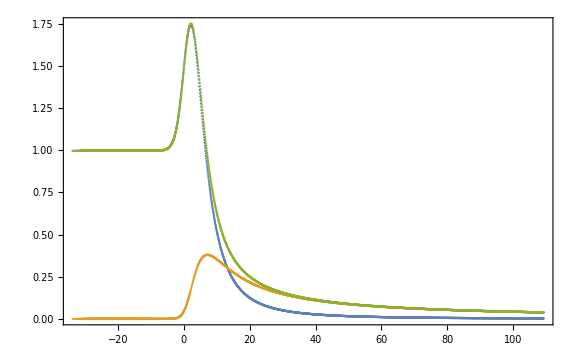

```mathematica
Clear@pts
pts[rule_]:=Table[(Thread@{rs,{Re@Veff,Im@Veff,Abs@Veff}}//.{r->y[x,25,(1+10^-15.)(1+Sqrt[1-a^2]),2]}∪rule),{x,0,1,0.001}]~Join~Table[(Thread@{rs,{Re@Veff,Im@Veff,Abs@Veff}}/.rule),{r,2,100,0.05}]//Transpose;
ListPlot[pts[{M->1,a->0.999999,ω->0.998,ℰ->5(5+1),m->2,s->-2}],ImageSize->Large,Joined->False,PlotRange->All,Frame->True]
```

## Near-horizon approximation ω̄ x≪1 (also Ω̄ x≪1 and χ x≪1)

```mathematica
Eq1 = (EqTeukolsky//Together@*Expand)/. RuleNearApprox // Collect[#, {ℛ[_],Derivative[_][ℛ][_]}, FullSimplify] &
```

((-x λ (x+τ)-ⅈ s τ χ+χ^2) ℛ[x])/(x (x+τ))+(1+s) (2 x+τ) ℛ'[x]+x (x+τ) ℛ''[x]

```mathematica
Sol1=(ℛ[x]/.First[DSolve[Eq1==0,ℛ,x]]//FullSimplify[#1,{{l,s}∈Integers,l≥0}]&)/.RuleFuncExpansion//ExpandAll//FullSimplify//Expand//PowerExpand
```

x^(-s-(ⅈ χ)/τ) (x+τ)^((ⅈ χ)/τ) C[1] Hypergeometric2F1[1/2 (1-√((1+2 s)^2+4 λ)),1/2 (1+√((1+2 s)^2+4 λ)),1-s-(2 ⅈ χ)/τ,-x/τ]+x^(-s/2) (x+τ)^(-s/2) C[2] LegendreQ[1/2 (-1+√((1+2 s)^2+4 λ)),s+(2 ⅈ χ)/τ,1+(2 x)/τ]

```mathematica
EqH=Eq1/(x^α(x+τ)^β)/.{ℛ->Function[x,x^α(x+τ)^β H[x]]}//FullSimplify//Collect[Expand@#,{x^(_.) Derivative[_][H][x],(x^(_.) H[x])/(x (x+τ))},FullSimplify]&
```

((x (α+β) (1+2 s+α+β)-x λ+(α+3 s α+2 α^2+β+s β+2 α β-λ) τ) H[x])/(x+τ)+((α (s+α) τ^2-ⅈ s τ χ+χ^2) H[x])/(x (x+τ))+2 x (1+s+α+β) H'[x]+(1+s+2 α) τ H'[x]+x^2 H''[x]+x τ H''[x]

```mathematica
SolβH=Equal@@(Coefficient[Coefficient[Simplify@ExpandAll[EqH x(x+τ)],H[x]],#]&/@{x^2,x τ})//First@DeleteCases[Solve[#,β],{β->α}]&;
SolαH=Coefficient[Simplify@ExpandAll[(x (x+τ))/H[x] EqH/.SolβH],x,0]//Expand@Solve[#==0,α]&;
SolαβH=Join[#,SolβH/.#]&/@SolαH
```

{{α→-s-(ⅈ χ)/τ,β→(ⅈ χ)/τ},{α→(ⅈ χ)/τ,β→-s-(ⅈ χ)/τ}}

```mathematica
{EqH1,EqH2}=EqH/.SolαβH//Collect[#,{H[_],Derivative[_][H][x]},Cancel@*Simplify]&
```

{(-s-s^2-λ) H[x]+(2 x+τ-s τ-2 ⅈ χ) H'[x]+x (x+τ) H''[x],(-s-s^2-λ) H[x]+(2 x+τ+s τ+2 ⅈ χ) H'[x]+x (x+τ) H''[x]}

```mathematica
Hypergeometric2F1[a,b,c,x]==Hypergeometric2F1[b,a,c,x]
```

True

```mathematica
SolABC=FullSimplify[First@Solve[{a+b+1==Coefficient[#,x H'[x]],a b==Coefficient[#,H[x]],c τ ==Coefficient[#,H'[x]]/.x->0},{a,b,c}]/.RuleEigenApprox,l>0]&/@{EqH1,EqH2}
```

{{a→-l,b→1+l,c→1-s-(2 ⅈ χ)/τ},{a→-l,b→1+l,c→1+s+(2 ⅈ χ)/τ}}

```mathematica
SolNfull= x^α(x+τ)^β Hypergeometric2F1[a,b,c,-x/τ]/.Join@@@Transpose[{SolαβH,SolABC}]//Simplify
```

{x^(-s-(ⅈ χ)/τ) (x+τ)^((ⅈ χ)/τ) Hypergeometric2F1[-l,1+l,1-s-(2 ⅈ χ)/τ,-x/τ],x^((ⅈ χ)/τ) (x+τ)^(-s-(ⅈ χ)/τ) Hypergeometric2F1[-l,1+l,1+s+(2 ⅈ χ)/τ,-x/τ]}

```mathematica
SolNear={𝒜 ,0}.SolNfull
```

x^(-s-(ⅈ χ)/τ) 𝒜 (x+τ)^((ⅈ χ)/τ) Hypergeometric2F1[-l,1+l,1-s-(2 ⅈ χ)/τ,-x/τ]

## Far-horizon approximation x≫τ

```mathematica
Eq2=ExpandAll[FullSimplify[EqTeukolskyRadial𝒦/x^2]/.Rule𝒦Radial//.RuleFarApprox]/.{a_ x^n_:>0/;n≤-3}//Collect[Simplify[#*x^2],{ℛ[x],ℛ'[x],ℛ''[x]}]&
```

(-λ+2 ⅈ s x ω̄+x^2 (ω̄)^2) ℛ[x]+2 (1+s) x ℛ'[x]+x^2 ℛ''[x]

```mathematica
EqG=Eq2/(x^α Exp[ζ I x ω̄])/.{ℛ->Function[x,x^α Exp[ζ I x ω̄]G[x]]}//FullSimplify//Collect[#/x/.ζ^2->1,Derivative[n_.][G][x],Simplify@*Expand]&
```

(G[x] (α+2 s α+α^2-λ+2 ⅈ x (s+ζ+s ζ+α ζ) ω̄))/x+2 (1+s+α+ⅈ x ζ ω̄) G'[x]+x G''[x]

```mathematica
SolαG=Solve[Coefficient[EqG,G[x]/x]==0/.x->0,α]/.RuleEigenApprox//FullSimplify[#,l> 0]&
```

{{α→-1-l-s},{α→l-s}}

```mathematica
{EqG1,EqG2}=Eq2/.SolαG/.RuleEigenApprox//FullSimplify
```

{(-l (1+l)+s+s^2+x ω̄ (2 ⅈ s+x ω̄)) ℛ[x]+x (2 (1+s) ℛ'[x]+x ℛ''[x]),(-l (1+l)+s+s^2+x ω̄ (2 ⅈ s+x ω̄)) ℛ[x]+x (2 (1+s) ℛ'[x]+x ℛ''[x])}

```mathematica
SolFfull=x^α Exp[ζ I ω̄ x]Hypergeometric1F1[(1+α+s)+ζ s,2(1+s+α),-2 ⅈ ζ x ω̄]/.SolαG
```

{ⅇ^(ⅈ x ζ ω̄) x^(-1-l-s) Hypergeometric1F1[-l+s ζ,-2 l,-2 ⅈ x ζ ω̄],ⅇ^(ⅈ x ζ ω̄) x^(l-s) Hypergeometric1F1[1+l+s ζ,2 (1+l),-2 ⅈ x ζ ω̄]}

```mathematica
SolFar=SolFfull.{𝒟,𝒞}/.ζ->-1
```

ⅇ^(-ⅈ x ω̄) x^(-1-l-s) 𝒟 Hypergeometric1F1[-l-s,-2 l,2 ⅈ x ω̄]+ⅇ^(-ⅈ x ω̄) x^(l-s) 𝒞 Hypergeometric1F1[1+l-s,2 (1+l),2 ⅈ x ω̄]

```mathematica
(Eq2/.{ℛ->Function[x,SolFar//Evaluate]}//FullSimplify)/.ζ^2->1
```

ⅇ^(-ⅈ x ω̄) x^(-1-l-s) (l+l^2-s (1+s)-λ) (𝒟 Hypergeometric1F1[-l-s,-2 l,2 ⅈ x ω̄]+x^(1+2 l) 𝒞 Hypergeometric1F1[1+l-s,2 (1+l),2 ⅈ x ω̄])

```mathematica
Series[SolFfull/.ζ->-1,{x,∞,0}]//Normal//Collect[(Expand@#)/.x^n_:>0/;((n/.s->0)<-1),x^_ Exp[_],Simplify]&
```

{(2^(l+s) ⅇ^(-ⅈ x ω̄) Gamma[-2 l] (-ⅈ ω̄)^(l+s))/(x Gamma[-l+s])+(2^(l-s) ⅇ^(ⅈ x ω̄) x^(-1-2 s) Gamma[-2 l] (ⅈ ω̄)^(l-s))/Gamma[-l-s],(2^(-1-l+s) ⅇ^(-ⅈ x ω̄) Gamma[2+2 l] (-ⅈ ω̄)^(-1-l+s))/(x Gamma[1+l+s])+(2^(-1-l-s) ⅇ^(ⅈ x ω̄) x^(-1-2 s) Gamma[2+2 l] (ⅈ ω̄)^(-1-l-s))/Gamma[1+l-s]}

## Matching of coefficients

```mathematica
SolNearSeriesFar=SolNear//Normal@Series[#/.{x+τ->x},{x,∞,0}]&//Collect[#,x^_,FullSimplify]&
```

(x^(-1-l-s) 𝒜 (1/τ)^(-1-l) Gamma[-1-2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[-l] Gamma[-((l+s) τ+2 ⅈ χ)/τ])+(2^(-3-2 l) x^(-2-l-s) 𝒜 (1/τ)^(-2-l) Gamma[-1/2-l] Gamma[1-s-(2 ⅈ χ)/τ])/(√π Gamma[-((1+l+s) τ+2 ⅈ χ)/τ])+(2^(-3+2 l) (-1+l) x^(-2+l-s) 𝒜 (1/τ)^(-2+l) Gamma[-1/2+l] Gamma[1-s-(2 ⅈ χ)/τ])/(√π Gamma[-1+l-s-(2 ⅈ χ)/τ])+(2^(-1+2 l) x^(-1+l-s) 𝒜 (1/τ)^(-1+l) Gamma[1/2+l] Gamma[1-s-(2 ⅈ χ)/τ])/(√π Gamma[l-s-(2 ⅈ χ)/τ])+(x^(l-s) 𝒜 (1/τ)^l Gamma[1+2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[1+l] Gamma[1+l-s-(2 ⅈ χ)/τ])

```mathematica
SolFarSeriesNear=SolFar//Normal@Series[#,{x,0,0}]&//Collect[#,x^_,FullSimplify]&
```

x^(-1-l-s) 𝒟+(x^(-l-s) 𝒟 ω̄ (6 ⅈ s+(x ω̄ (3 (-1+l) (l-2 s^2)-ⅈ s (1-3 l+2 s^2) x ω̄))/((-1+l) (-1+2 l))))/(6 l)+x^(l-s) (𝒞+(x 𝒞 ω̄ (-2 ⅈ (3+2 l) s-(1+l+2 s^2) x ω̄))/(2 (1+l) (3+2 l)))

```mathematica
SeriesMatchExponents=Intersection@@(DeleteDuplicates@Cases[ExpandAll@#,b_ x^n_->n]&/@{SolNearSeriesFar,SolFarSeriesNear})
```

{-1-l-s,l-s}

```mathematica
x^SeriesMatchExponents
```

{x^(-1-l-s),x^(l-s)}

```mathematica
Subtract@@((x^SeriesMatchExponents).(Coefficient[#,x^SeriesMatchExponents]/.{x^(_.)->0})&/@{SolNearSeriesFar,SolFarSeriesNear})
```

-x^(l-s) 𝒞-x^(-1-l-s) 𝒟+(x^(-1-l-s) 𝒜 (1/τ)^(-1-l) Gamma[-1-2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[-l] Gamma[-((l+s) τ+2 ⅈ χ)/τ])+(x^(l-s) 𝒜 (1/τ)^l Gamma[1+2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[1+l] Gamma[1+l-s-(2 ⅈ χ)/τ])

```mathematica
EqsCoefFarNear= Subtract@@((Coefficient[#,x^SeriesMatchExponents]/.{x^(_.)->0})&/@{SolNearSeriesFar,SolFarSeriesNear})
```

{-𝒟+(𝒜 (1/τ)^(-1-l) Gamma[-1-2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[-l] Gamma[-((l+s) τ+2 ⅈ χ)/τ]),-𝒞+(𝒜 (1/τ)^l Gamma[1+2 l] Gamma[1-s-(2 ⅈ χ)/τ])/(Gamma[1+l] Gamma[1+l-s-(2 ⅈ χ)/τ])}

```mathematica
RuleMatching=EqsCoefFarNear//PowerExpand@First@Solve[Eliminate[Thread[#==0/.{𝒞->1}],𝒜],𝒟]/.RuleNegativeΓ&
```

{𝒟→((-1)^(1+l) τ^(1+2 l) Gamma[1+l]^2 Gamma[1+l-s-(2 ⅈ χ)/τ])/(2 Gamma[1+2 l] Gamma[2+2 l] Gamma[-((l+s) τ+2 ⅈ χ)/τ])}

## Power at infinity

```mathematica
SolFarSeriesFar=(SolFar//Normal@Series[#,{x,∞,0}]&//ExpandAll)/.{x^α_/;If[NumberQ[α],α<-1,α+2 s<-1]->0}
```

(2^(l+s) ⅇ^(-ⅈ x ω̄) 𝒟 Gamma[-2 l] (-ⅈ ω̄)^(l+s))/(x Gamma[-l+s])+(2^(l-s) ⅇ^(ⅈ x ω̄) x^(-1-2 s) 𝒟 Gamma[-2 l] (ⅈ ω̄)^(l-s))/Gamma[-l-s]+(ⅈ 2^(-1-l+s) ⅇ^(-ⅈ x ω̄) 𝒞 Gamma[2+2 l] (-ⅈ ω̄)^(-l+s))/(x Gamma[1+l+s] ω̄)-(ⅈ 2^(-1-l-s) ⅇ^(ⅈ x ω̄) x^(-1-2 s) 𝒞 Gamma[2+2 l] (ⅈ ω̄)^(-l-s))/(Gamma[1+l-s] ω̄)

```mathematica
{Ain,Aout}=SolFarSeriesFar//Coefficient[#,{ⅇ^(-ⅈ x ω̄) x^-1,ⅇ^(ⅈ x ω̄) x^(-1-2 s)}].DiagonalMatrix[{rp,rp^(1+2s)}]&
```

{rp ((2^(l+s) 𝒟 Gamma[-2 l] (-ⅈ ω̄)^(l+s))/Gamma[-l+s]+(ⅈ 2^(-1-l+s) 𝒞 Gamma[2+2 l] (-ⅈ ω̄)^(-l+s))/(Gamma[1+l+s] ω̄)),rp^(1+2 s) ((2^(l-s) 𝒟 Gamma[-2 l] (ⅈ ω̄)^(l-s))/Gamma[-l-s]-(ⅈ 2^(-1-l-s) 𝒞 Gamma[2+2 l] (ⅈ ω̄)^(-l-s))/(Gamma[1+l-s] ω̄))}

```mathematica
((-1)^(l+1)Gamma[l+2])/(4 (ω̄)^2 Gamma[l])Aout/(rp^(2s)Ain)//.RuleMatching∪{𝒞->1,s->-1}∪RuleNegativeΓ//Together//PowerExpand//Simplify[#,l∈Integers]&
```

(2 Gamma[1+2 l]^2 Gamma[2+2 l]^2 Gamma[1-l-(2 ⅈ χ)/τ]+4^l Gamma[l] Gamma[1+l]^2 Gamma[2+l] Gamma[2+l-(2 ⅈ χ)/τ] (ⅈ τ ω̄)^(1+2 l))/(2 Gamma[1+2 l]^2 Gamma[2+2 l]^2 Gamma[1-l-(2 ⅈ χ)/τ]-4^l Gamma[l] Gamma[1+l]^2 Gamma[2+l] Gamma[2+l-(2 ⅈ χ)/τ] (ⅈ τ ω̄)^(1+2 l))

```mathematica
Gamma[1+l+s-x]Gamma[1+l-s+x]/Product[k^2-x^2,{k,s,l}]//FullSimplify[#,{l∈Integers,s∈Integers,x∈Reals,l≥Abs[s]}]&
```

(Gamma[s-x] Gamma[1+l+s-x] Gamma[1+l-s+x] Gamma[s+x])/(Gamma[1+l-x] Gamma[1+l+x])

## Relation between Φ_0 and Φ_2 or Ψ_0 and Ψ_4

```mathematica
InOutSimplify=Factor@FullSimplify[ComplexExpand[#,Subscript[_, in]|Subscript[_, hole]|Subscript[_, out]|𝒞],x>0]/.{κ->χ/(2M),ϵ->τ/(8M)}&;
```

```mathematica
Rfar[s_]:=(Subscript[A, in] ⅇ^(-ⅈ ω̄ x) x^-1+Subscript[A, out]  ⅇ^(ⅈ ω̄ x) x^(-1-2s))/.If[s>0,{A->𝒴},{A->𝒵}];
Rnear[s_]:= Subscript[A, hole](x)^(-s-(ⅈ χ)/τ)  (x+τ)^-s/.If[s>0,{A->𝒴},{A->𝒵}];
```

#### Spin 1

```mathematica
InRelation1= (D[#, x]-I ω̄#&)@(D[#, x]-I ω̄#&)@Rfar[-1]-ℬ Rfar[1]//Simplify//Normal@Series[#,{x,∞,1}]&//Coefficient[#,ⅇ^(-ⅈ x ω̄) x^-1]&
```

-ℬ 𝒴_in-4 (ω̄)^2 𝒵_in

```mathematica
OutRelation1=x^2(D[#, x]+I ω̄#&)@(D[#, x]+I ω̄#&)@(x^2 Rfar[1])-ℬ Rfar[-1]//Normal@Series[#,{x,∞,0}]&//Coefficient[Expand@#,ⅇ^(ⅈ x ω̄)x]&
```

-4 (ω̄)^2 𝒴_out-ℬ 𝒵_out

```mathematica
HoleRelation1=(D[#, x]-(ⅈ χ)/(τ x) #&)@*(D[#, x]-(ⅈ χ)/(τ x) #&)@Rnear[-1]-ℬ Rnear[1]//Simplify//Normal@Series[x^(1+(ⅈ χ)/τ) # τ,{x,0,0}]&//FullSimplify
```

-ℬ 𝒴_hole-2 ⅈ (τ-2 ⅈ χ) χ 𝒵_hole

```mathematica
{RelationYZ1,RelationZY1}=First@Solve[{OutRelation1==0,InRelation1==0,HoleRelation1==0},#]&/@{{Subscript[𝒴, out],Subscript[𝒴, in],Subscript[𝒴, hole]},{Subscript[𝒵, out],Subscript[𝒵, in],Subscript[𝒵, hole]}}//FullSimplify
```

{{𝒴_out→-(ℬ 𝒵_out)/(4 (ω̄)^2),𝒴_in→-(4 (ω̄)^2 𝒵_in)/ℬ,𝒴_hole→-(2 ⅈ (τ-2 ⅈ χ) χ 𝒵_hole)/ℬ},{𝒵_out→-(4 (ω̄)^2 𝒴_out)/ℬ,𝒵_in→-(ℬ 𝒴_in)/(4 (ω̄)^2),𝒵_hole→(ⅈ ℬ 𝒴_hole)/(2 τ χ-4 ⅈ χ^2)}}

```mathematica
{Ein1,Eout1,Ehole1}=1/4{x^2 Abs[Rfar[1]]^2,x^2 Abs[Rfar[-1]/x^2]^2,(ω̄)/(κ rp)(2M rp) Abs[(rp^2 x(x+τ)Rnear[1]/rp)/(2*(2M rp))]^2}//InOutSimplify//Coefficient[#,x,0]&
```

{1/4 Abs[𝒴_in]^2,1/4 Abs[𝒵_out]^2,(Abs[𝒴_hole]^2 ω̄)/(16 χ)}

```mathematica
{Ehole1/Ein1,Eout1/Ehole1,Eout1/Ein1}/.{RelationZY1,RelationYZ1}/.{Subscript[_, hole]-> 1}//InOutSimplify//(#/.{Subscript[x_, y_]:>ToExpression[ToString[x/.{𝒵->Z,𝒴->Y}]<>ToString[y]]})&
```

{{(ω̄)/(4 χ Abs[Yin]^2),(64 χ Abs[Yout]^2 (ω̄)^3)/ℬ^2,(16 Abs[Yout]^2 (ω̄)^4)/(ℬ^2 Abs[Yin]^2)},{(χ (τ^2+4 χ^2))/(16 Abs[Zin]^2 (ω̄)^3),(ℬ^2 Abs[Zout]^2)/(χ (τ^2+4 χ^2) ω̄),(ℬ^2 Abs[Zout]^2)/(16 Abs[Zin]^2 (ω̄)^4)}}

### Spin 2

```mathematica
InRelation2=Nest[(D[#, x]-ⅈ ω̄#&),Rfar[-2],4]-𝒞 Rfar[2]//Normal@Series[#,{x,∞,0}]&//Coefficient[Expand@#,ⅇ^(-ⅈ x ω̄)x^-1]&
```

-𝒞 𝒴_in+16 (ω̄)^4 𝒵_in

```mathematica
OutRelation2=x^4 Nest[(D[#, x]+ⅈ ω̄#&),x^4 Rfar[2],4]-𝒞* Rfar[-2]//Expand//Normal@Series[#,{x,∞,0}]&//Coefficient[#,ⅇ^(ⅈ x ω̄) x^3]&
```

16 (ω̄)^4 𝒴_out-Conjugate[𝒞] 𝒵_out

```mathematica
HoleRelation2=Nest[(D[#, x]-(ⅈ χ)/(τ x) #&),Rnear[-2],4]-𝒞 Rnear[2]//Simplify//Normal@Series[ τ^2 x^(+2+(ⅈ χ)/τ)#,{x,0,0}]&//FullSimplify
```

-𝒞 𝒴_hole+4 (τ-2 ⅈ χ) (τ+2 ⅈ χ) χ (ⅈ τ+χ) 𝒵_hole

```mathematica
{RelationYZ2,RelationZY2}=First@Solve[{OutRelation2==0,InRelation2==0,HoleRelation2==0},#]&/@{{Subscript[𝒴, out],Subscript[𝒴, in],Subscript[𝒴, hole]},{Subscript[𝒵, out],Subscript[𝒵, in],Subscript[𝒵, hole]}}//FullSimplify//Factor
```

{{𝒴_out→(Conjugate[𝒞] 𝒵_out)/(16 (ω̄)^4),𝒴_in→(16 (ω̄)^4 𝒵_in)/𝒞,𝒴_hole→(4 (τ-ⅈ χ) (τ+2 ⅈ χ) χ (ⅈ τ+2 χ) 𝒵_hole)/𝒞},{𝒵_out→(16 (ω̄)^4 𝒴_out)/Conjugate[𝒞],𝒵_in→(𝒞 𝒴_in)/(16 (ω̄)^4),𝒵_hole→(𝒞 𝒴_hole)/(4 (ⅈ τ-2 χ) (τ-ⅈ χ) (τ-2 ⅈ χ) χ)}}

```mathematica
{Ein2,Eout2,Ehole2}={x^2/(32(ω̄)^2)Abs[Rfar[2]]^2,x^2/(2(ω̄)^2)Abs[Rfar[-2]/(4 x^4)]^2,(ω̄ M)/κ Abs[((x(x+τ)rp^2)^2 Rnear[2]/rp^2)/(4(2M rp)^2(I κ+2 ϵ))]^2}//InOutSimplify//Coefficient[#,x,0]&//Factor
```

{Abs[𝒴_in]^2/(32 (ω̄)^2),Abs[𝒵_out]^2/(32 (ω̄)^2),(Abs[𝒴_hole]^2 ω̄)/(8 χ (τ^2+4 χ^2))}

```mathematica
{Ehole2/Ein2,Eout2/Ehole2,Eout2/Ein2}/.{RelationZY2,RelationYZ2}/.{Subscript[_, hole]-> 1}//InOutSimplify//(#/.{Subscript[x_, y_]:>ToExpression[ToString[x/.{𝒵->Z,𝒴->Y}]<>ToString[y]]})&
```

{{(4 (ω̄)^3)/(χ (τ^2+4 χ^2) Abs[Yin]^2),(64 χ (τ^2+4 χ^2) Abs[Yout]^2 (ω̄)^5)/Abs[𝒞]^2,(256 Abs[Yout]^2 (ω̄)^8)/Abs[Yin 𝒞]^2},{(χ (τ^2+χ^2) (τ^2+4 χ^2))/(4 Abs[Zin]^2 (ω̄)^5),(𝒞 Abs[Zout]^2 Conjugate[𝒞])/(64 χ (τ^2+χ^2) (τ^2+4 χ^2) (ω̄)^3),(𝒞 Abs[Zout]^2 Conjugate[𝒞])/(256 Abs[Zin]^2 (ω̄)^8)}}

## Relation with numerical ansatz

```mathematica
AllRelationAntsatz1=Flatten[{
Rnear[1]-𝒶[0] x^(-1-(ⅈ χ)/τ)//First@Solve[Normal@Series[#/x^(-1-(ⅈ χ)/τ),{x,0,0}]==0,Subscript[𝒴, hole]]&,
Rnear[-1]-𝒷[0] x^(1-(ⅈ χ)/τ)//First@Solve[Normal@Series[#/x^(-1-(ⅈ χ)/τ),{x,0,0}]==0,Subscript[𝒵, hole]]&,
(Rfar[1]-fp x^(-1-(ⅈ χ)/τ))/.{ω r->ω̄ x+ω̄(2-τ) Log[x],r->rp x}//First@Solve[Coefficient[x^(1+(ⅈ χ)/τ)#,x,0]==0,Subscript[𝒴, in]]&,
(Rfar[-1]-fm x^(1-(ⅈ χ)/τ))/.{ω r->ω̄ x+ω̄(2-τ) Log[x],r->rp x}//First@Solve[Coefficient[x^(-1+(ⅈ χ)/τ)#,x,0]==0,Subscript[𝒵, out]]&}
]/.{x^(Complex[0,-1] β_)->ⅇ^(ⅈ β HoldForm@Log[x])}
```

{𝒴_hole→rp τ 𝒶[0],𝒴_in→ⅇ^(ⅈ x ω̄) fp rp x^(-(ⅈ χ)/τ+ⅈ (2-τ) ω̄),𝒵_out→(ⅇ^(-ⅈ x ω̄) fm x^(-(ⅈ χ)/τ-ⅈ (2-τ) ω̄))/rp}

```mathematica
AllRelationAntsatz2=Flatten[{
Rnear[2]-𝒶[0] x^(-2-(ⅈ χ)/τ)//First@Solve[Normal@Series[#/x^(-2-(ⅈ χ)/τ),{x,0,0}]==0,Subscript[𝒴, hole]]&,
Rnear[-2]-𝒷[0] x^(2-(ⅈ χ)/τ)//First@Solve[Normal@Series[#/x^(2-(ⅈ χ)/τ),{x,0,0}]==0,Subscript[𝒵, hole]]&,
(Rfar[2]-fp x^(-2-(ⅈ χ)/τ))/.{ω r->ω̄ x+ω̄(2-τ) Log[x],r->rp x}//First@Solve[Normal@Series[#,{x,∞,0}]==0,Subscript[𝒴, in]]&,
(Rfar[-2]-fm x^(2-(ⅈ χ)/τ))/.{ω r->ω̄ x+ω̄(2-τ) Log[x],r->rp x}//First@Solve[Normal@Series[x^-4#//Expand,{x,∞,0}]==0,Subscript[𝒵, out]]&}
]/.{x^(Complex[0,-1] β_)->ⅇ^(ⅈ β HoldForm@Log[x])}
```

{𝒴_hole→rp^2 τ^2 𝒶[0],𝒵_hole→𝒷[0]/(rp^2 τ^2),𝒴_in→ⅇ^(ⅈ x ω̄) fp rp x^(-1-(ⅈ χ)/τ+2 ⅈ ω̄-ⅈ τ ω̄),𝒵_out→(ⅇ^(-ⅈ x ω̄) fm x^(-1-(ⅈ χ)/τ-2 ⅈ ω̄+ⅈ τ ω̄))/rp^3}

```mathematica
Eout2/Ein2/.AllRelationAntsatz2//ComplexExpand[#,fm|fp]&//FullSimplify[#,x>0]&
```

(fm Conjugate[fm])/(rp^8 Abs[fp]^2)

```mathematica
Ehole2/Ein2/.AllRelationAntsatz2//ComplexExpand[#,fm|fp]&//FullSimplify[#,x>0]&//Factor
```

(4 x^2 τ^4 ω^3 𝒶[0]^2)/(fp rp χ (τ^2+4 χ^2) Conjugate[fp])

```mathematica
Eout2/Ehole2/.AllRelationAntsatz2//ComplexExpand[#,fm|fp]&//FullSimplify[#,x>0]&//Factor
```

(fm χ (τ^2+4 χ^2) Conjugate[fm])/(4 rp^7 x^2 τ^4 ω^3 𝒶[0]^2)

```mathematica
Integrate[(x(x+2)+(2-τ))/(x(x+τ)),x]//Series[#,{x,∞,0}]&//Simplify
```

x-(-2+τ) Log[x]+O[1/x]^1

```mathematica
Integrate[(x(x+2)+(2-τ))/(x(x+τ)),x]//Series[#,{x,∞,0}]&
```

x+(2 Log[x]-τ Log[x])+O[1/x]^1

```mathematica
Divide@@{1/4 Abs[Subscript[𝒵, out]]^2,1/4 Abs[Subscript[𝒴, in]]^2}/.AllRelationAntsatz1//Simplify[ComplexExpand@#,x>0]&
```

fm^2/(fp^2 rp^4)

```mathematica
Divide@@{(ω̄)/(4 χ rp^2)Abs[Subscript[𝒴, hole]]^2,1/4 Abs[Subscript[𝒴, in]]^2}/.AllRelationAntsatz1//Simplify[ComplexExpand@#,x>0]&
```

(τ^2 ω̄ 𝒶[0]^2)/(fp^2 rp^2 χ)

```mathematica
Divide@@{1/4 Abs[Subscript[𝒵, out]]^2,(ω̄)/(4 χ rp^2)Abs[Subscript[𝒴, hole]]^2}/.AllRelationAntsatz1//Simplify[ComplexExpand@#,x>0]&
```

(fm^2 χ)/(rp^2 τ^2 ω̄ 𝒶[0]^2)

```mathematica
Divide@@{1/4 Abs[Subscript[𝒵, out]]^2,(ω̄)/(4 χ rp^2)Abs[Subscript[𝒴, hole]]^2}/.First@Solve[HoleRelation1==0,Subscript[𝒴, hole]]/.AllRelationAntsatz1//Factor@FullSimplify[ComplexExpand@#,x>0]&
```

(fm^2 ℬ^2)/(4 χ (τ^2+4 χ^2) ω̄ 𝒵_hole^2)

## MST formalism

### Horizon Hypergeometric function series

```mathematica
EqMSTin=((Δ[r]^-s D[(Δ[r]^(s+1)R'[r]), r]+((𝒦[r]^2-2I s(r-M)𝒦[r])/Δ[r]+4I s ω r-λ)R[r])/.{R[r]->R[z],Derivative[n_][R][r]:>(-1/(2 κ M))^n Derivative[n][R][z],r->rp-2M z κ,a^2->2 M rp-rp^2}//Simplify)/.{rp->(1+κ)M,a->((2M ω-κ τ)/m)M }//Collect[#,{R[_],Derivative[_][R][_]},(Collect[#/.{ω->ϵ/(2M)},ϵ,FullSimplify]&)]&
```

((ϵ^2 (1-2 z+2 (-1+z) z κ)^2)/(4 (-1+z) z)+(ϵ (-ⅈ s (1+2 (-1+z) z (-1+2 z) κ)+τ+2 z (-1+(-1+z) κ) τ))/(2 (-1+z) z)+(-4 (-1+z) z λ+2 ⅈ s (-1+2 z) τ+τ^2)/(4 (-1+z) z)) R[z]+(1+s) (-1+2 z) R'[z]+(-1+z) z R''[z]

```mathematica
AnsatzMSTin={R->Function[x,Exp[I κ ϵ x](-x)^(-s-I(ϵ+τ)/2)(1-x)^(I (ϵ-τ)/2)P[x]]};
```

```mathematica
EqMSTPin=P[z] EqMSTin/R[z]/.AnsatzMSTin//Simplify[{0,-#}+(#/.ϵ->0)+(λ+s (s+1)-ν (ν+1)) P[z]+I ϵ P'[z]]&;
EqMSTPin[[1]]//Collect[#,{P[_],Derivative[_][P][_]},Simplify]&
EqMSTPin[[2]]//Collect[#,ϵ,Simplify]&
```

(-ν-ν^2-τ (ⅈ+τ)) P[z]+(s+z (2-2 ⅈ τ)+ⅈ (ⅈ+ϵ+τ)) P'[z]+(-1+z) z P''[z]

ϵ^2 (-1+2 z κ) P[z]+(s+s^2+λ-ν (1+ν)) P[z]+ⅈ ϵ κ ((1+2 s (-1+z)-2 z+2 ⅈ z τ) P[z]-2 (-1+z) z P'[z])

```mathematica
MSTseriesInLHS=Simplify[EqMSTPin⟦1⟧/.{P''[z]->(-(c-(a+b+1) z) P'[z]+a b P[z])/(z (1-z))}/.{a->n+ν+1-ⅈ τ,b->-n-ν-ⅈ τ,c->1-s-ⅈ ϵ-ⅈ τ}]/.P[z]->𝒶[n]p[n+ν]
```

n (1+n+2 ν) p[n+ν] 𝒶[n]

```mathematica
MSTseriesInRHS=Expand@EqMSTPin⟦2⟧/.{
z P[z]->(-(m+1-s-I ϵ)(m+1-I τ))/(2(m+1)(2m+1))𝒶[n]p[n+ν+1]+1/2(1+((s+I ϵ)I τ)/(m(m+1)))𝒶[n]p[n+ν]-((m+s+I ϵ)(m+I τ))/(2m(2m+1))𝒶[n]p[n+ν-1], P'[z]->1/(z (1-z))(((m+I τ)(m+1-I τ)(m+1-s-I ϵ))/(2(m+1)(2m+1))𝒶[n]p[n+ν+1]+1/2(s+I ϵ)(1+(I τ(1-I τ))/(m(m+1)))𝒶[n]p[n+ν]-((m+1-I τ)(m+I τ)(m+s+I ϵ))/(2m(2m+1))𝒶[n]p[n+ν-1])}//FullSimplify[#/.{P[z]->𝒶[n]p[n+ν],m->n+ν}]&;
```

```mathematica
RuleMSTSeriesInCoef={α[ν_,n_],β[ν_,n_],γ[ν_,n_]}:> Evaluate@(MSTseriesInRHS-MSTseriesInLHS//Cases[Collect[#,_p,Simplify],α_ 𝒶[n]p[ν+β_]:>(α/.{n->2n-β})]&//FullSimplify)//Thread
```

{α[ν_,n_]:>-(ⅈ ϵ κ (ϵ^2+(1+n+s+ν)^2) (1+n+ν+ⅈ τ))/((1+n+ν) (3+2 n+2 ν)),β[ν_,n_]:>s (1+s)-ϵ^2+λ-ν-ν^2-n (1+n+2 ν)-(ϵ κ (n+n^2+s^2+ϵ^2+ν+2 n ν+ν^2) τ)/((n+ν) (1+n+ν)),γ[ν_,n_]:>(ϵ κ (n-s-ⅈ ϵ+ν) (n-s+ⅈ ϵ+ν) (ⅈ (n+ν)+τ))/((n+ν) (-1+2 n+2 ν))}

```mathematica
ℋ[l_]=(2(l^2-m^2)(l^2-s^2)^2)/((2l-1)l^3(2l+1));
ℛ[ν_,n_,M_]:=-Fold[γ[ν,n+#2]/(β[ν,n+#2]-α[ν,n+#2]#1)&,γ[ν,n+M+1],Reverse@Range[0,M]]
ℒ[ν_,n_,M_]:=-Fold[α[ν,n-#2]/(β[ν,n-#2]-γ[ν,n-#2]#1)&,γ[ν,n+M+1],Reverse@Range[0,M]]
```

```mathematica
(β[ν,n]+α[ν,n]ℛ[ν,n+1,3]+γ[ν,n]ℒ[ν,n-1,3])/.{n->0}/.RuleMSTSeriesInCoef//.{τ->(ϵ-m 𝒿)/κ,λ->l(l+1)-s(s+1)+(𝒿 ϵ/2)^2-m 𝒿 ϵ+f[1]𝒿 ϵ/2+f[2](𝒿 ϵ/2)^2+f[3](𝒿 ϵ/2)^3,κ->Sqrt[1-𝒿^2],ν->l+β[2] ϵ^2+ β[3] ϵ^3,f[1]->(-2m s^2)/(l(l+1)),f[2]->H[l+1]-H[l]-1,f[3]->-2m s^2(ℋ[l+1]/(l(l+1)^2(l+2))-ℋ[l]/((l-1)l^2(l+1)))}//Series[#,{ϵ,0,3}]&//First@Solve[Coefficient[#1,{ϵ^2,ϵ^3}]==0,{β[2],β[3]}]&//FullSimplify
```

{β[2]→-1/(4 (-1-2 l))(-8-(4 s^2)/(l+l^2)+𝒿^2+(2 (l-s)^2 (l+s)^2 (-m^2 𝒿^2+l^2 (-1+𝒿^2)))/(l^3 (-1+4 l^2))+(2 (1+l-s)^2 (1+l+s)^2 (m^2 𝒿^2-(1+l)^2 (-1+𝒿^2)))/((1+l)^3 (3+4 l (2+l)))+𝒿^2 (-1-H[l]+H[1+l])),β[3]→(m 𝒿 (4 l^3 (1+l)^3 ((-1+l) l (1+l) (2+l) (-3+5 l (1+l))+(11+3 l (1+l) (-3+l+l^2)) s^2+(-16+3 l (1+l)) s^4+5 s^6)+2 (-1+l) (2+l) s^2 ((l+l^2)^3 (-1+l+l^2+m^2)+2 (l+l^2)^2 (l+l^2-3 m^2) s^2+(-3 l^2 (1+l)^2+(3+5 l (1+l)) m^2) s^4) 𝒿^2+(-1+l) l^3 (1+l)^3 (2+l) (-1+2 l) (3+2 l) s^2 𝒿^2 (H[l]-H[1+l])))/(4 (-1+l) l^5 (1+l)^5 (2+l) (-1+2 l) (1+2 l) (3+2 l))}

### Outer Coulomb wave function series

```mathematica
EqMSTout=((Δ[r]^-s D[(Δ[r]^(s+1)R'[r]), r]+((𝒦[r]^2-2I s(r-M)𝒦[r])/Δ[r]+4I s ω r-λ)R[r])/.{R[r]->R[z],Derivative[n_][R][r]:>(ϵ/(2M))^n Derivative[n][R][z],r->M(1-κ)+2M z/ϵ,a^2->2 M rp-rp^2}//Simplify)/.{rp->(1+κ)M,a->((2M ω-κ τ)/m)M }//Collect[#/.{ω->ϵ/(2M)},{R[_],Derivative[_][R][_]},Simplify]&
```

1/(4 z (z-ϵ κ))(4 z^4-8 z^3 ϵ (-1+κ)+ϵ^2 κ^2 (ϵ-τ)^2+4 z^2 (ϵ^2 (1-3 κ+κ^2)-λ+ϵ κ τ)+2 ⅈ s (4 z^3-6 z^2 ϵ κ+2 z ϵ κ (ϵ κ-τ)+ϵ^2 κ^2 (-ϵ+τ))+4 z ϵ κ (ϵ^2 (-1+κ)+λ+ϵ (τ-κ τ))) R[z]+(1+s) (2 z-ϵ κ) R'[z]+z (z-ϵ κ) R''[z]

```mathematica
AnsatzMSTout={R->Function[x,x^(-1-s)(1-(ϵ κ)/x)^(-s-I(ϵ+τ)/2)F[x]]};
```

```mathematica
EqMSTPout=F[z] EqMSTout/R[z]/.AnsatzMSTout//Simplify[{0,-#}+(#/.ϵ->0)+(λ+s (s+1)-ν (ν+1)) F[z]+2ϵ z F[z]]&;
EqMSTPout[[1]]//Collect[#,{Derivative[_][F][_],F[_]},Simplify]&
EqMSTPout[[2]]//Collect[ExpandAll@#,{ϵ κ z F''[z],ϵ κ z F[z],F'[z],z^-1 F[z],F[z]},Simplify]&
```

(2 ⅈ s z+z^2+2 z ϵ-ν (1+ν)) F[z]+z^2 F''[z]

z ϵ κ F[z]-(ϵ (ⅈ-ⅈ s+ϵ) κ (ⅈ+τ) F[z])/z+(s+s^2+ϵ^2 (-1+κ)+ⅈ s ϵ κ+λ-ν-ν^2-ϵ κ τ) F[z]+ϵ κ (s+ⅈ (ⅈ+ϵ+τ)) F'[z]+z ϵ κ F''[z]

```mathematica
F[z]/.First@DSolve[0==EqMSTPout[[1]],F,z]//FunctionExpand[#]/.{√(s-ⅈ ϵ)->-(-1)^(-3/4)√(-I(s-ⅈ ϵ))}&//Simplify[#/.C[2]->0]&
```

2^(1+ν) ⅇ^(-ⅈ z) (ⅈ z)^(1+ν) C[1] Hypergeometric1F1[1-s+ⅈ ϵ+ν,2+2 ν,2 ⅈ z]

```mathematica
f[l_,η_]=(Exp[-I #] 2^l#^(l+1)*Gamma[l+1-I η]/Gamma[2l+1]*Hypergeometric1F1[l+1-I η,2l+2,2I #]&);
```

```mathematica
MSTseriesOutLHS=(EqMSTPout[[1]]/.{F->f[ν+n,-I s-ϵ]})/(f[ν+n,-I s-ϵ][z])//FullSimplify[#  ℊ[n]f[ν+n]]&
```

n (1+n+2 ν) f[n+ν] ℊ[n]

```mathematica
MSTseriesOutRHS=EqMSTPout[[2]]/.{F''[z]->(-1+FullSimplify[((F''[z]+F[z])/.{F->f[ν+n,-I s-ϵ]})/(f[ν+n,-I s-ϵ][z])])F[z]}//Collect[Expand@#,{F'[z],z^-1 F[z],F[z]},FullSimplify]&//Simplify[#/.{F'[z]->
-(m(m+1+s-I ϵ))/((m+1)(2m+1)) ℊ[n]f[m+1]+((I s+ϵ)/(m(m+1))) ℊ[n]f[m]+((m+1)(m-s+I ϵ))/(m(2m+1)) ℊ[n]f[m-1],z^-1 F[z]->(m+1+s-I ϵ)/((m+1)(2m+1)) ℊ[n]f[m+1]+(I s+ϵ)/(m(m+1)) ℊ[n]f[m]+(m-s+I ϵ)/(m(2m+1)) ℊ[n]f[m-1]}/.{m->n+ν,F[z]->ℊ[n]f[ν+n]}]&
```

(((n+ν) (1+n+ν) (1+2 (n+ν)) (s+s^2-ⅈ s ϵ κ+λ-ν (1+ν)-ϵ (ϵ+ϵ κ+κ τ)) f[n+ν]+ϵ κ (1+n+n^2-s-ⅈ ϵ+ν+2 n ν+ν^2+ⅈ (-1+s+ⅈ ϵ) τ) ((1+n+ν) (n-s+ⅈ ϵ+ν) f[-1+n+ν]+(ⅈ s+ϵ) (1+2 (n+ν)) f[n+ν]+(n+ν) (1+n+s-ⅈ ϵ+ν) f[1+n+ν])+ϵ κ (s+ⅈ (ⅈ+ϵ+τ)) ((1+n+ν)^2 (n-s+ⅈ ϵ+ν) f[-1+n+ν]+(ⅈ s+ϵ) (1+2 (n+ν)) f[n+ν]-(n+ν)^2 (1+n+s-ⅈ ϵ+ν) f[1+n+ν])) ℊ[n])/((n+ν) (1+n+ν) (1+2 (n+ν)))

```mathematica
RuleMSTSeriesOutCoef={α[ν_,n_],β[ν_,n_],γ[ν_,n_]}:> Evaluate@(MSTseriesOutRHS-MSTseriesOutLHS//Cases[Collect[#,_f,Simplify],α_ ℊ[n]f[ν+β_]:>(α/.{n->2n-β})]&//FullSimplify)//Thread
```

{α[ν_,n_]:>(ϵ κ (1+n-s+ⅈ ϵ+ν) (1+n+s+ⅈ ϵ+ν) (1+n+ν+ⅈ τ))/((1+n+ν) (3+2 n+2 ν)),β[ν_,n_]:>-n-n^2+s+s^2-ϵ^2+λ-ν-2 n ν-ν^2-(ϵ κ (n+n^2+s^2+ϵ^2+ν+2 n ν+ν^2) τ)/((n+ν) (1+n+ν)),γ[ν_,n_]:>(ϵ κ (n-s-ⅈ ϵ+ν) (n+s-ⅈ ϵ+ν) (n+ν-ⅈ τ))/((n+ν) (-1+2 n+2 ν))}

```mathematica
(-γ[ν,n]f[n+ν,η][z])/(4n β[ν,n]f[n+ν+1,η][z])/.RuleMSTSeriesOutCoef//FullSimplify//FirstCase[{#},α_ Hypergeometric1F1[a_,b_,z_](Hypergeometric1F1[a0_,b0_,z_])^-1:>α Sum[z^k/(k!)Normal@Series[Pochhammer[k,a]/Pochhammer[k,b],{n,∞,1}],{k,0,∞}]/Sum[z^k/(k!)Normal@Series[Pochhammer[k,a0]/Pochhammer[k,b0],{n,∞,2}],{k,0,∞}]]&//Series[#,{n,∞,1}]&
```

(ϵ κ)/z-(ⅈ ϵ κ (2 ϵ-η+τ))/(z n)+O[1/n]^2

```mathematica
Hypergeometric1F1[a,c,z]==Gamma[c]/Gamma[c-a] Exp[I a π]HypergeometricU[a,c,x]+Gamma[c]/Gamma[a] Exp[I (c-a) π]Exp[x]HypergeometricU[c-a,c,-x]//FullSimplify
```

Hypergeometric1F1[a,c,z]==Gamma[c] ((ⅇ^(ⅈ a π) HypergeometricU[a,c,x])/Gamma[-a+c]+(ⅇ^(ⅈ (-a+c) π+x) HypergeometricU[-a+c,c,-x])/Gamma[a])

```mathematica
Hypergeometric1F1[a,c,z]//Series[#,{z,∞,0}]&//Normal@Collect[#,z,Simplify]&
```

(ⅇ^z z^(a-c) Gamma[c])/Gamma[a]+((-1)^-a z^-a Gamma[c])/Gamma[-a+c]

```mathematica
Gamma[c]{(ⅇ^(-ⅈ a π) HypergeometricU[a,c,z])/Gamma[-a+c],(ⅇ^(ⅈ (-a+c) π+z) HypergeometricU[-a+c,c,-z])/Gamma[a]}//Normal@Series[#,{z,∞,0}]&//Collect[#,z,Simplify]&
```

{(ⅇ^(-ⅈ a π) z^-a Gamma[c])/Gamma[-a+c],(ⅇ^z z^(a-c) Gamma[c])/Gamma[a]}